```mathematica
Homework for Chapter 3-1& 3-2
```

## 2012311804 이병호 / 2016314728 정재헌

(#1) 다음의 연립일차방정식의 해를 구하시오.
                                        x+2y+4z=3,
                                        3x+4y+5z=7,
                                        x+3y+4z=4.

```mathematica
f1=x+2y+4z==3
f2=3x+4y+5z==7
f3=x+3y+4z==4
Solve[{f1,f2,f3},{x,y,z}]
```

x+2 y+4 z==3

3 x+4 y+5 z==7

x+3 y+4 z==4

{{x→1,y→1,z→0}}

(#2) 타원 x^2/4+y^2/9=1  과 포물선 y=x^2-4 을 그리고  그 교차점을 구하시오.

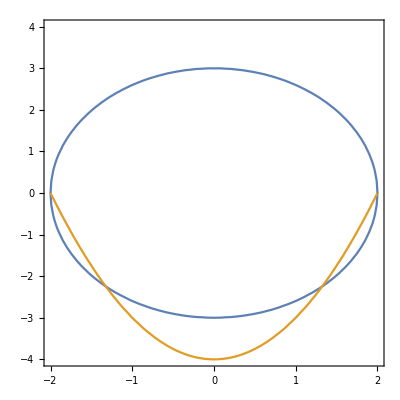

```mathematica
ContourPlot[{(x^2)/4+(y^2)/9==1, x^2-4==y},{x,-2,2},{y,-4,4}]
```

```mathematica
f4=(x^2)/4+(y^2)/9==1
f5= x^2-4==y
Solve[{f4,f5},{x,y}]
```

x^2/4+y^2/9==1

-4+x^2==y

{{x→-2,y→0},{x→2,y→0},{x→-(√7)/2,y→-9/4},{x→(√7)/2,y→-9/4}}

(#3) 비선형 방정식 cot x=2x 의 처음 5개의 양의 근을 Table 함수(statement)를 사용하여 구하시오.

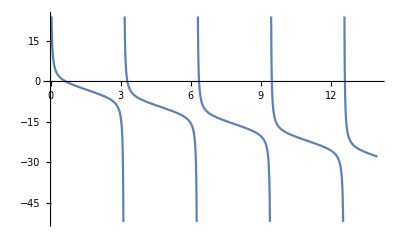

```mathematica
Plot[Cot[x]==2x,{x,0,14}]
```

```mathematica
Table[FindRoot[Cot[x]==2x,{x,π*i}],{i,0.1,5}]
```

{{x→0.653271},{x→3.29231},{x→6.36162},{x→9.47749},{x→3.29231}}

(#4) Secant method를 교재에서와 같이 While 명령어를 사용하여 구현하고 교재와 동일한 함수에 적용한 예를 보이시오.

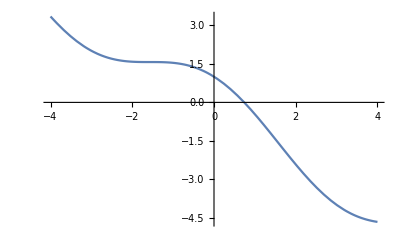

```mathematica
Plot[Cos[x]-x==0, {x,-4,4}]
```

```mathematica
ssecant[func_,u_,v_,ϵ_, Max_]:= (
{x1=u, x2=v, n=0, app={}};
While[Abs[func[x1]]>ϵ&&n<Max,n=n+1;x1=x1-(x1-x2)/(func[x1]-func[x2])*func[x1]//N;
app=Append[app,{n,x1,func[x1]}]
];
TableForm[app, TableHeadings->{{"Secant Method"}, {"n","x","f(x)"}}]
)
```

```mathematica
g[x_]:=Cos[x]-x;
ssecant[g,0,2,0.000001,30]
```

| n | x | f(x)
Secant Method | 1 | 0.585455 | 0.248006
 | 2 | 0.717135 | 0.036557
 | 3 | 0.736256 | 0.00473244
 | 4 | 0.738726 | 0.000600825
 | 5 | 0.73904 | 0.0000760875
 | 6 | 0.739079 | 9.63251×10^-6
 | 7 | 0.739084 | 1.2194×10^-6
 | 8 | 0.739085 | 1.54367×10^-7

(#5) 다음 함수를 plot한 후  f(x)=tan x +x 의 처음 10개의 양의 근  λ_n을  (1) FindRoot 와  (2) Secant method로 찾고   이 값을  이용하여  다음 함수를  plot하시오.
                                               ∑_(n=1)^10 ⅇ^(-(λ_n)^2t) sin(λ_n x)      for  0<t <1,  0<x<1.

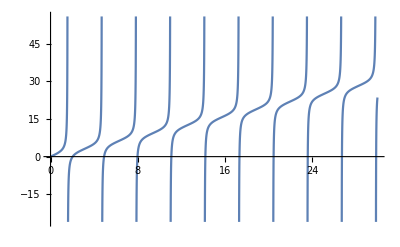

```mathematica
Plot[Tan[x]+x==0,{x,0,30}]
```

```mathematica
Table[FindRoot[Tan[x]==-x,{x,π*i}],{i,0.6,10}]
```

{{x→2.02876},{x→4.91318},{x→7.97867},{x→11.0855},{x→14.2074},{x→17.3364},{x→20.4692},{x→23.6043},{x→26.7409},{x→29.8786}}

```mathematica
Sols={2.02876, 4.91318, 7.97867, 11.0855, 14.2074, 17.3364, 20.4692, 23.6043, 26.7409, 29.8786}
```

{2.02876,4.91318,7.97867,11.0855,14.2074,17.3364,20.4692,23.6043,26.7409,29.8786}

```mathematica
Clear[g]
```

```mathematica
g[x_]:=Tan[x] + x;
Table[ssecant[g,3.141592*i,3.1416/2,0.0000001,10],{i,1,10}]
```

{ | n | x | f(x)
Secant Method | 1 | 3.14157 | 3.14156
 | 2 | 3.14156 | 3.14152
 | 3 | 3.14154 | 3.14148
 | 4 | 3.14152 | 3.14145
 | 5 | 3.1415 | 3.14141
 | 6 | 3.14148 | 3.14137
 | 7 | 3.14147 | 3.14134
 | 8 | 3.14145 | 3.1413
 | 9 | 3.14143 | 3.14127
 | 10 | 3.14141 | 3.14123, | n | x | f(x)
Secant Method | 1 | 6.28308 | 6.28297
 | 2 | 6.28297 | 6.28275
 | 3 | 6.28286 | 6.28253
 | 4 | 6.28275 | 6.28231
 | 5 | 6.28264 | 6.2821
 | 6 | 6.28253 | 6.28188
 | 7 | 6.28242 | 6.28166
 | 8 | 6.28231 | 6.28144
 | 9 | 6.28221 | 6.28123
 | 10 | 6.2821 | 6.28101, | n | x | f(x)
Secant Method | 1 | 9.4245 | 9.42423
 | 2 | 9.42423 | 9.42369
 | 3 | 9.42396 | 9.42314
 | 4 | 9.42369 | 9.4226
 | 5 | 9.42342 | 9.42206
 | 6 | 9.42315 | 9.42151
 | 7 | 9.42287 | 9.42097
 | 8 | 9.4226 | 9.42043
 | 9 | 9.42233 | 9.41988
 | 10 | 9.42206 | 9.41934, | n | x | f(x)
Secant Method | 1 | 12.5659 | 12.5654
 | 2 | 12.5654 | 12.5643
 | 3 | 12.5648 | 12.5633
 | 4 | 12.5643 | 12.5623
 | 5 | 12.5638 | 12.5613
 | 6 | 12.5633 | 12.5603
 | 7 | 12.5628 | 12.5593
 | 8 | 12.5623 | 12.5582
 | 9 | 12.5618 | 12.5572
 | 10 | 12.5613 | 12.5562, | n | x | f(x)
Secant Method | 1 | 15.7071 | 15.7063
 | 2 | 15.7063 | 15.7047
 | 3 | 15.7055 | 15.7031
 | 4 | 15.7047 | 15.7014
 | 5 | 15.7039 | 15.6998
 | 6 | 15.7031 | 15.6982
 | 7 | 15.7023 | 15.6965
 | 8 | 15.7014 | 15.6949
 | 9 | 15.7006 | 15.6933
 | 10 | 15.6998 | 15.6917, | n | x | f(x)
Secant Method | 1 | 18.8484 | 18.8472
 | 2 | 18.8472 | 18.8448
 | 3 | 18.846 | 18.8424
 | 4 | 18.8448 | 18.84
 | 5 | 18.8436 | 18.8376
 | 6 | 18.8424 | 18.8352
 | 7 | 18.8412 | 18.8328
 | 8 | 18.84 | 18.8304
 | 9 | 18.8388 | 18.828
 | 10 | 18.8376 | 18.8256, | n | x | f(x)
Secant Method | 1 | 21.9895 | 21.9878
 | 2 | 21.9878 | 21.9845
 | 3 | 21.9862 | 21.9812
 | 4 | 21.9845 | 21.9779
 | 5 | 21.9829 | 21.9747
 | 6 | 21.9813 | 21.9714
 | 7 | 21.9796 | 21.9681
 | 8 | 21.978 | 21.9648
 | 9 | 21.9763 | 21.9615
 | 10 | 21.9747 | 21.9582, | n | x | f(x)
Secant Method | 1 | 25.1306 | 25.1284
 | 2 | 25.1284 | 25.124
 | 3 | 25.1262 | 25.1197
 | 4 | 25.124 | 25.1153
 | 5 | 25.1219 | 25.111
 | 6 | 25.1197 | 25.1066
 | 7 | 25.1175 | 25.1023
 | 8 | 25.1154 | 25.098
 | 9 | 25.1132 | 25.0936
 | 10 | 25.111 | 25.0893, | n | x | f(x)
Secant Method | 1 | 28.2716 | 28.2688
 | 2 | 28.2688 | 28.2632
 | 3 | 28.266 | 28.2577
 | 4 | 28.2632 | 28.2521
 | 5 | 28.2605 | 28.2466
 | 6 | 28.2577 | 28.2411
 | 7 | 28.2549 | 28.2355
 | 8 | 28.2522 | 28.23
 | 9 | 28.2494 | 28.2245
 | 10 | 28.2466 | 28.2189, | n | x | f(x)
Secant Method | 1 | 31.4125 | 31.409
 | 2 | 31.409 | 31.4021
 | 3 | 31.4056 | 31.3953
 | 4 | 31.4022 | 31.3884
 | 5 | 31.3987 | 31.3815
 | 6 | 31.3953 | 31.3746
 | 7 | 31.3918 | 31.3677
 | 8 | 31.3884 | 31.3609
 | 9 | 31.385 | 31.354
 | 10 | 31.3815 | 31.3471}

```mathematica
f[t_,x_]=∑_(i=1)^10 ⅇ^(-(Sols[[i]])^2*t)Sin[Sols[[i]]*x]
```

ⅇ^(-4.11587 t) Sin[2.02876 x]+ⅇ^(-24.1393 t) Sin[4.91318 x]+ⅇ^(-63.6592 t) Sin[7.97867 x]+ⅇ^(-122.888 t) Sin[11.0855 x]+ⅇ^(-201.85 t) Sin[14.2074 x]+ⅇ^(-300.551 t) Sin[17.3364 x]+ⅇ^(-418.988 t) Sin[20.4692 x]+ⅇ^(-557.163 t) Sin[23.6043 x]+ⅇ^(-715.076 t) Sin[26.7409 x]+ⅇ^(-892.731 t) Sin[29.8786 x]

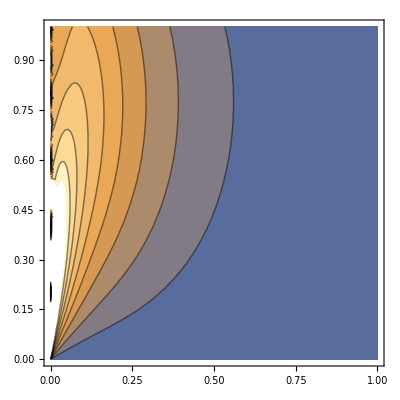

```mathematica
ContourPlot[f[t,x],{t,0,1},{x,0,1}]
```